## Scattering lengths according to Innsbruck and Rice papers.

```mathematica
ainns[B_]:=Module[
{abg=-1405 ,
Bo=834 , 
Δ=300 ,
α=4*^-4 }  ,
abg(1+Δ/(B-Bo))(1+α(B-Bo))
]
```

```mathematica
arice[B_]:=Module[
{abg=-1580 ,
Bo=834 , 
Δ=270 },  
abg(1+Δ/(B-Bo))]
```

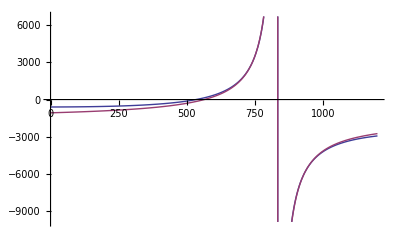

```mathematica
Plot[{ainns[B], arice[B]},{B,0,1200}]
```

```mathematica
toFile[fun_,labels_]:=Module[{head,stream},
dat=Table[{B,fun[B]},{B,0.,830.,1.}];
SetDirectory[NotebookDirectory[]];
head="#"<>labels[[1]]<>"\t"<>labels[[2]]<>"\n";
stream=OpenWrite[ToString[fun]<>".dat"];
WriteString[stream, head<>ExportString[dat,"Table"]];
Close[stream];
]
```

```mathematica
toFile[ainns,{"bfield(Gauss)","ainns(a0)"}]
toFile[arice,{"bfield(Gauss)","arice(a0)"}]
```